# Gyroscopes

## Nicholas Stroughair

Summer 2021

## Making JD+

### Global Values

#### Changeable values

h = height of gyroscope, l = width of gyroscope, k should be set at 1 for gyroscope array to be rectangular, which is necessary for cylinder gluing :
----------------------------------------------------------------------------------------

```mathematica
h =11;
l= 11;
k=1;
α = 1;
β = 1;
γ = 0.1;
λ = 2.5757541984847983;
```

#### Projection Matrices

Defining Projections for pu=up projection, pnw = northwest projection, pne=northeast projection, put = orthogonal up projection, etc :
--------------------------------------------------------------------------------

```mathematica
pu = {{0,0},{0,1}};
pnw= {{3/4,-Sqrt[3]/4},{-Sqrt[3]/4,1/4}};
pne= {{3/4,Sqrt[3]/4},{Sqrt[3]/4,1/4}};
put = {{1,0},{0,0}};
pnwt= {{1/4,Sqrt[3]/4},{Sqrt[3]/4,3/4}};
pnet= {{1/4,-Sqrt[3]/4},{-Sqrt[3]/4,3/4}};
```

#### General Lattice Functions: --------------------------------------

these functions test whether an edge is NE NW Ver respectively
---------------------------------------------------------------------------------

```mathematica
vTest[{a_,b_}]:=a-b=={0,2}||a-b=={0,-2}
nwTest[{a_,b_}]:=a-b=={√3,-1}||a-b==-{√3,-1}
neTest[{a_,b_}]:=a-b=={-√3,-1}||a-b=={√3,1}
```

Functions to generate details on a given hexagonal array.

hexgrid Generates the background graph, one should note that all the functions following are fundamentally the same with just a different output, I am sure there is a better way to handle this but have yet to implement it.
------------------------------------------------------------------------

```mathematica
hexGrid[{wide1_Integer?Positive,wide2_Integer?Positive,wide3_Integer?Positive},opts:OptionsPattern[Graph]]:=Module[{cells,edges,vertices},cells=Flatten[Table[CirclePoints[{Sqrt[3] (1 j+k-2)+Sqrt[3] (1 j+l-2),3 k-2-3 l},{2,π/2},6],{j,wide1},{k,wide2},{l,wide3}],2];
edges=Union[Sort/@Flatten[Partition[#,2,1,1]&/@cells,1]];
vertices=Sort[Union[Flatten[edges,1]],#1[[2]]>#2[[2]]&];
IndexGraph[Graph[UndirectedEdge@@@edges,opts,VertexCoordinates->Thread[vertices->vertices]]]]
```

hexPoints outputs the coordinates of the hexagonal lattice  
--------------------------------------------------------------------------

```mathematica
hexPoints[{wide1_Integer?Positive,wide2_Integer?Positive,wide3_Integer?Positive},opts:OptionsPattern[Graph]]:=Module[{cells,edges,vertices},cells=Flatten[Table[CirclePoints[{Sqrt[3] (1 j+k-2)+Sqrt[3] (1 j+l-2),3 k-2-3 l},{2,π/2},6],{j,wide1},{k,wide2},{l,wide3}],2];
edges=Union[Sort/@Flatten[Partition[#,2,1,1]&/@cells,1]];
vertices=Sort[Union[Flatten[edges,1]],#1[[2]]>#2[[2]]&];
vertices]
```

hexEdges out puts edges of lattice 
--------------------------------------------

```mathematica
hexEdges[{wide1_Integer?Positive,wide2_Integer?Positive,wide3_Integer?Positive},opts:OptionsPattern[Graph]]:=Module[{cells,edges,vertices},cells=Flatten[Table[CirclePoints[{Sqrt[3] (1 j+k-2)+Sqrt[3] (1 j+l-2),3 k-2-3 l},{2,π/2},6],{j,wide1},{k,wide2},{l,wide3}],2];
edges=Union[Sort/@Flatten[Partition[#,2,1,1]&/@cells,1]];
vertices=Sort[Union[Flatten[edges,1]],#1[[2]]>#2[[2]]&];
edges]
```

hexMat out puts Adjacency matrix, one should note that unlike the directional adjacency matrices, hexMat has no 1’ on the diagonal
--------------------------------------------------------------------------------------------

#### Directional Lattice functions: ---------------------------------------

The following functions separate out the various directions of the adjacency matrices, they also come with 1’s along the diagonal so as to maintain the ordering and degree.
-------------------------------------------------------------------------------------------

these functions test whether an edge is NE NW Ver respectively
---------------------------------------------------------------------------------

```mathematica
vTest[{a_,b_}]:=a-b=={0,2}||a-b=={0,-2}
nwTest[{a_,b_}]:=a-b=={√3,-1}||a-b==-{√3,-1}
neTest[{a_,b_}]:=a-b=={-√3,-1}||a-b=={√3,1}
```

the following are like the genera lattice functions but utilize the above tests to eliminate edges.
------------------------------------------------------------------------------------------------

```mathematica
hexVerticalMat[{wide1_Integer?Positive,wide2_Integer?Positive,wide3_Integer?Positive},opts:OptionsPattern[Graph]]:=Module[{cells,edges,vertices,verticaledges},cells=Flatten[Table[CirclePoints[{Sqrt[3] (1 j+k-2)+Sqrt[3] (1 j+l-2),3 k-2-3 l},{2,π/2},6],{j,wide1},{k,wide2},{l,wide3}],2];
edges=Union[Sort/@Flatten[Partition[#,2,1,1]&/@cells,1]];
vertices=Sort[Union[Flatten[edges,1]],#1[[2]]>#2[[2]]&];
verticaledges={};
For[i=0,i<Length[vertices],i++,AppendTo[verticaledges,{vertices[[i+1]],vertices[[i+1]]}]];
For[i=0,i<Length[edges],i++,If[vTest[edges[[i+1]]],AppendTo[verticaledges,edges[[i+1]]]]];
AdjacencyMatrix[Graph[UndirectedEdge@@@verticaledges,opts,VertexCoordinates->Thread[vertices->vertices]]]]
```

----------------------------------------------------------------------------------------------

```mathematica
hexNEMat[{wide1_Integer?Positive,wide2_Integer?Positive,wide3_Integer?Positive},opts:OptionsPattern[Graph]]:=Module[{cells,edges,vertices,needges},cells=Flatten[Table[CirclePoints[{Sqrt[3] (1 j+k-2)+Sqrt[3] (1 j+l-2),3 k-2-3 l},{2,π/2},6],{j,wide1},{k,wide2},{l,wide3}],2];
edges=Union[Sort/@Flatten[Partition[#,2,1,1]&/@cells,1]];
vertices=Sort[Union[Flatten[edges,1]],#1[[2]]>#2[[2]]&];
needges={};
For[i=0,i<Length[vertices],i++,AppendTo[needges,{vertices[[i+1]],vertices[[i+1]]}]];
For[i=0,i<Length[edges],i++,If[neTest[edges[[i+1]]],AppendTo[needges,edges[[i+1]]]]];
AdjacencyMatrix[Graph[UndirectedEdge@@@needges,opts,VertexCoordinates->Thread[vertices->vertices]]]]
```

--------------------------------------------------------------------------------------------------

```mathematica
hexNWMat[{wide1_Integer?Positive,wide2_Integer?Positive,wide3_Integer?Positive},opts:OptionsPattern[Graph]]:=Module[{cells,edges,vertices,nwedges},cells=Flatten[Table[CirclePoints[{Sqrt[3] (1 j+k-2)+Sqrt[3] (1 j+l-2),3 k-2-3 l},{2,π/2},6],{j,wide1},{k,wide2},{l,wide3}],2];
edges=Union[Sort/@Flatten[Partition[#,2,1,1]&/@cells,1]];
vertices=Sort[Union[Flatten[edges,1]],#1[[2]]>#2[[2]]&];
nwedges={};
For[i=0,i<Length[vertices],i++,AppendTo[nwedges,{vertices[[i+1]],vertices[[i+1]]}]];
For[i=0,i<Length[edges],i++,If[nwTest[edges[[i+1]]],AppendTo[nwedges,edges[[i+1]]]]];
AdjacencyMatrix[Graph[UndirectedEdge@@@nwedges,opts,VertexCoordinates->Thread[vertices->vertices]]]]
```

#### Misc Functions: ----------------------------------------

grabevec takes the output of Mathematica eigensystem and give you a eigen vector corresponding roughly to the value you enter (currently it will give out the largest eigenvalue less than 0.1+input)
----------------------------------------------------------------------------------------------------

```mathematica
grabevec[eigensystem_,eigenval_] :=
Module[ {eigenvec},
For[i=0,i<Length[eigensystem[[1]]],i++,If[Abs[eigensystem[[1,i]]-eigenval]<0.1,eigenvec =eigensystem[[2,i]]]];
eigenvec
]
```

addtwodeggrees takes a matrix and in-beds it in a matrix two degrees larger, this is so we can add the two extra points to finish the cylinder 
----------------------------------------------------------------------------------------------------

```mathematica
addtwodegrees[a_]:=
Module[{newarray,addones},
newarray = SparseArray[Band[{1,1}]->{a,ConstantArray[0,{2,2}]}];
newarray[[Length[newarray]-1,Length[newarray]-1]] = 1;
newarray[[Length[newarray],Length[newarray]]] = 1;
newarray
]
```

### Making Adjacency matrices:

begin to make matrices
-----------------------------

```mathematica
vAdj = hexVerticalMat[{h,l,k}];
neAdj = hexNEMat[{h,l,k}];
nwAdj = hexNWMat[{h,l,k}];
MatrixForm[vAdj]
```

(1)
 |  |  |  |

#### Cylinder Gluing -------------------

first we must add two extra points and glue them
--------------------------------------------------------------

```mathematica
neAdj= addtwodegrees[Normal[neAdj]];
nwAdj= addtwodegrees[Normal[nwAdj]];
vAdj= addtwodegrees[Normal[vAdj]];
```

Then we add the edges for these two points:
---------------------------------------------------------------

```mathematica
neAdj =neAdj+SparseArray[{{l+1,Length[neAdj]-1}-> 1,{Length[neAdj]-1,l+1}-> 1},{Length[neAdj],Length[neAdj]}];
nwAdj =nwAdj+SparseArray[{{2l+1,Length[neAdj]-1}-> 1,{Length[neAdj]-1,2l+1}-> 1},{Length[neAdj],Length[neAdj]}];
neAdj =neAdj+SparseArray[{{2h*l+2h+l,Length[neAdj]}-> 1,{Length[neAdj],2h*l+2h+l}-> 1},{Length[neAdj],Length[neAdj]}];
nwAdj =nwAdj+SparseArray[{{2h*l+2h,Length[neAdj]}-> 1,{Length[neAdj],2h*l+2h}-> 1},{Length[neAdj],Length[neAdj]}];
```

now we glue the rest of the side
---------------------------------------------

```mathematica
cylinder =SparseArray[Table[{(2l+2)t,(2l+2)t+(2l+1)}->1,{t,1,h-1}],{Length[nwAdj],Length[nwAdj]}];
cylinder = cylinder+Transpose[cylinder];
nwAdj = nwAdj+cylinder;
```

#### Torus Gluing -------------------

form list of top and bottom points
--------------------------------------------------------------

```mathematica
(*topedge = Table[i,{i,0,l}];
botedge = Mod[topedge-(h-1)/2,l+1]+(2h+1)(l+1);
topedge = topedge+1;
topedge [[l+1]] = Length[neAdj]-1;
For[i=0,i<Length[botedge],i++,If[botedge[[i]]==Length[neAdj]-1,botedge[[i]]=Length[neAdj]]];
torus = SparseArray[Table[ArrayReshape[Riffle[topedge,botedge],{l+1,2}][[i]]->1,{i,l+1}],{Length[neAdj],Length[neAdj]}];
torus = torus+Transpose[torus];
vAdj = vAdj+torus;*)
```

Test of Adjacency Matrix
---------------------------------

```mathematica
(*Method->"HighDimensionalEmbedding"*)
```

```mathematica
tAdj =nwAdj+neAdj+vAdj-3IdentityMatrix[Length[nwAdj]];
```

```mathematica
MatrixForm[tAdj];
```

```mathematica
GraphPlot3D[nwAdj];
GraphPlot3D[neAdj];
GraphPlot3D[vAdj];
```

```mathematica
(*AdjacencyGraph[vAdj+2neAdj+3nwAdj-6IdentityMatrix[Length[vAdj]]]*)
```

### Making D&J:

Format adjacency matrices properly, 1 on diagonals and -1 if they have an edge connecting them 
----------------------------------------------------------------------------------------------------

```mathematica
modVAdj = IdentityMatrix[Length[vAdj]]-vAdj;
modNEAdj = IdentityMatrix[Length[vAdj]] -neAdj;
modNWAdj = IdentityMatrix[Length[vAdj]]-nwAdj; 
For[i=0,i<Length[modNWAdj],If[Norm[modNWAdj[[i]]]>0,modNWAdj[[i,i]]=1],i++];
For[i=0,i<Length[modNEAdj],If[Norm[modNEAdj[[i]]]>0,modNEAdj[[i,i]]=1],i++];
For[i=0,i<Length[modVAdj],If[Norm[modVAdj[[i]]]>0,modVAdj[[i,i]]=1],i++];
```

```mathematica
GraphPlot3D[ -modVAdj-modNWAdj-modNEAdj+3IdentityMatrix[Length[vAdj]]];
```

Tensor with projections, vmat = vertical etc and netmat = NE orthogonal etc
----------------------------------------------------------------------------------------------

```mathematica
vmat = ArrayFlatten[TensorProduct[modVAdj,pu]];
nemat = ArrayFlatten[TensorProduct[modNEAdj,pne]];
nwmat = ArrayFlatten[TensorProduct[modNWAdj,pnw]];
vtmat = ArrayFlatten[TensorProduct[modVAdj,put]];
netmat = ArrayFlatten[TensorProduct[modNEAdj,pnet]];
nwtmat = ArrayFlatten[TensorProduct[modNWAdj,pnwt]];
```

Defines final matrices
--------------------------

```mathematica
dPd = vmat + nemat + nwmat;
dPtd = vtmat + netmat + nwtmat;
(*jmat = DiagonalMatrix[ConstantArray[-1,Length[vmat]-1],1]+DiagonalMatrix[ConstantArray[1,Length[vmat]-1],-1];*)
jmat = ArrayFlatten[TensorProduct[IdentityMatrix[Length[vAdj]],{{0,-1},{1,0}}]];
dmat = SparseArray[α IdentityMatrix[Length[dPd]]+γ dPd+β dPtd];
MatrixForm[jmat];
```

## Graphs & Stuff

### Movies and graphs:

#### Misc Functions ----------------------

grabevec takes the output of Mathematica eigensystem and give you a eigen vector corresponding roughly to the value you enter (currently it will give out the largest eigenvalue less than 0.1+input)
----------------------------------------------------------------------------------------------------

```mathematica
grabevec[eigensystem_,eigenval_] :=
Module[ {eigenvec},
For[i=0,i<Length[eigensystem[[1]]],i++,If[Abs[eigensystem[[1,i]]-eigenval]<0.1,eigenvec =eigensystem[[2,i]]]];
eigenvec
]
```

#### Math for Movie --------------------

first we define the initial position
--------------------------------------------------------------

```mathematica
(*{3.065076,3.0479659999999997,3.019958,2.981792,2.934452,2.87912,2.817125,2.7498679999999998,2.6787669999999997,2.60518,2.530348,2.4553409999999998,2.3810189999999998,2.308005,2.23668,2.167192,2.099484,2.033339,1.968457,1.9056309999999999,1.968457,2.033339,2.099484,2.167192,2.23668,2.308005,2.3810189999999998,2.4553409999999998,2.530348,2.60518,2.6787669999999997,2.7498679999999998,2.817125,2.87912,2.934452,2.981792,3.019958,3.0479659999999997,3.065076,3.0708309999999996}*)
```

```mathematica
inPos =Round[ grabevec[ Eigensystem[I jmat.dmat],1.5],0.00000001];
(*inPos = ConstantArray[0,Length[dmat]];
inPos[[1]]=0.01;*)
```

We now define our position function, The Real is to remove some rounding bug, and the array re-shapes the output from a vector to a list of points.
pos was original, pos2 takes an initial position and acts on it, pos3 wiggles the point in the top right.
----------------------------------------------

```mathematica
(*pos[t_,inPos_] := ArrayReshape[[MatrixExp[(jmat.dmat)*t,inPos]+MatrixExp[(jmat.dmat)*(-t),Conjugate[inPos]]],{Length[dmat]/2,2}]*)
```

```mathematica
pos[t_,inPos_] := ArrayReshape[Im[MatrixExp[(jmat.dmat)*t,inPos]],{Length[dmat]/2,2}]
```

```mathematica
pos2[size_,number_,initialPositions_]:=Module[{positions,length},
positions = {};
length = Length[dmat];
AppendTo[positions,initialPositions];
For[i=1,i<number,i++,
positions =AppendTo[positions, ArrayReshape[Re[MatrixExp[(jmat.dmat)*size,Flatten[positions[[i]]]]],{length/2,2}]]];
positions
]
```

```mathematica
pos3[size_,number_]:=Module[{positions,length},
positions = {};
length = Length[dmat];
AppendTo[positions,ArrayReshape[inPos, {length/2,2}]];
For[i=1,i<number,i++,
positions[[i,1,1]]=Sin[i*size*2.5757541984847983]/10;
positions =AppendTo[positions, ArrayReshape[Re[MatrixExp[(jmat.dmat)*size,Flatten[positions[[i]]]]],{length/2,2}]]];
positions
]
```

#### Guessing Solution --------------------

define Amplitude function acting like a soliton
--------------------------------------------------------------

```mathematica
amplitude[x_,t_]:= (3/2)Max[Table[(1/5)E^(-1/2((x+i(2l+2))/5+t)^2),{i,-10,10}]]
```

We now define our position function guess
----------------------------------------------

```mathematica
rot = 8;
```

```mathematica
topRow[i_,t_]:= amplitude[1+2(l-i),t]{Cos [λ rot t+(i+1)Pi],Sin[λ rot t+(i+1)Pi]}
bottomRow[i_,t_]:=(1/3)amplitude[2(l+1-i),t]{0,Cos[λ rot t+(i+1)Pi]}
guessSolution[t_]:= Module[{topPositions,bottomPositions,otherPositions,positionsGuess},
topPositions = Table[topRow[i,t*stepsize],{i,1,l}];
bottomPositions = Table[bottomRow[i,t*stepsize],{i,1,l+1}];
otherPositions = ConstantArray[{0,0},Length[dmat]/2-2l-3];
AppendTo[otherPositions,topRow[l+1,t*stepsize]];
AppendTo[otherPositions,{0,0}];
positionsGuess =Join[topPositions,bottomPositions,otherPositions];
positionsGuess
]
```

#### Functions that generate the frames of the Movie -----------------------------------------------------------------

colour table takes list of points and attaches a hue based on how large their norm is.
-------------------------------------------------------------------------------------------------

```mathematica
colourtable[listofpts_] :=
Module[ {colourlist},
colourlist= {};
For[i=1,i<=Length[listofpts],i++,
colourlist = AppendTo[colourlist,Hue[Norm[listofpts[[i]]]]]];
colourlist
]
```

takes list of points and creates one frame of a movie
--------------------------------------------------------------------

```mathematica
graphpts[listofpts_,label_]:= 
Module[{data},
data = ArrayReshape[Riffle[listofpts,6*listofpts+hexpts],{Length[listofpts],4}];
Show[Graphics[{Hue[Norm[{#1,#2}]],PointSize[Log[Norm[{#1,#2}]+1.1]/8],Point[{#3,#4}]}&@@@data,Background->LightGray,PlotLabel->label],hexg,PlotRange->{{minx-2,maxx+2},{miny-2,maxy+2}}]
]
```

```mathematica
edgeSoliton[listofpts_]:= 
Module[{data,cutpts,cuthex},
cutpts = Take[listofpts,2l];
cuthex = Take[hexpts,2l];
data = ArrayReshape[Riffle[cutpts,cuthex],{Length[listofpts],4}];
Graphics[{Hue[Norm[{#1,#2}]],PointSize[0.01],Point[{#3,30*Norm[{#1,#2}]}]}&@@@data,Background->Black,PlotRange->{{minx+6,maxx+2},{0,20}}]
]
```

#### Movie Details -------------------

Saves some outputs 
---------------------------

```mathematica
hexpts=hexPoints[{h,l,k}];
AppendTo[hexpts,hexpts[[l+1]]+{Sqrt[3],1}];
AppendTo[hexpts,hexpts[[(2h)(l+1)]]+{Sqrt[3],-1}];

maxx = Max[hexpts[[All,1]]];
minx = Min[hexpts[[All,1]]];
maxy = Max[hexpts[[All,2]]];
miny = Min[hexpts[[All,2]]];

hexg=hexGrid[{h,l,k}];
```

Makes frames for the movie, Sorry for the mess.
--------------------------------------------------------------------------------------------------

```mathematica
stepsize=1/10;
numberofsteps = 200;

frames = Table[graphpts[2*pos[i*stepsize,inPos],"BulkEigenvalue"],{i,0,numberofsteps}];

(*positions1 = pos3[stepsize,numberofsteps];
positions2 = pos2[stepsize,4*numberofsteps,positions1[[numberofsteps]]];
frames1 = Table[edgeSoliton[positions1[[i]]],{i,1,Length[positions1]}];
frames2= Table[edgeSoliton[positions2[[i]]],{i,1,Length[positions2]}];
frames = Join[frames1,frames2];*)
(*topandbottomPositions = Table[guessSolution[t*stepsize],{t,0,numberofsteps}];
positions1 = pos3[stepsize,numberofsteps];
positions2 = pos2[stepsize,4numberofsteps,topandbottomPositions[[numberofsteps]]];
positions21=pos2[stepsize,4*numberofsteps,positions1[[numberofsteps]]];
positions3 = Join[topandbottomPositions,positions2];
positions4 = Join[positions1,positions21];
frames3 = Table[graphpts[positions1[[i]],"wiggle"],{i,1,Length[positions1]}];
frames4 = Table[graphpts[positions21[[i]],"No External Force "],{i,1,Length[positions21]}];
frames5 = Table[graphpts[topandbottomPositions[[i]],"guess"],{i,1,Length[topandbottomPositions]}];
frames6 = Table[graphpts[positions2[[i]],"No External Force "],{i,1,Length[positions2]}];*)
```

```mathematica
(*frameswiggle = Join[frames3,frames4];
framesguess = Join[frames5,frames6];*)
```

Animates the frames,
----------------------------

```mathematica
movie =Manipulate[Show[frames[[n]]],{n,1,Length[frames],1,Animator,AnimationRate->10*numberofsteps,AnimationRunning->False,DisplayAllSteps->True}]
```

#### Histogram -------------------

Makes a Histogram 
---------------------------

```mathematica
(*Histogram[Abs[ Eigenvalues[Normal[I jmat.dmat]]],80]*)
```

```mathematica
(*Export[NotebookDirectory[]<>"wiggleinmiddle.avi",movie,"AnimationDuration"->180]*)
```

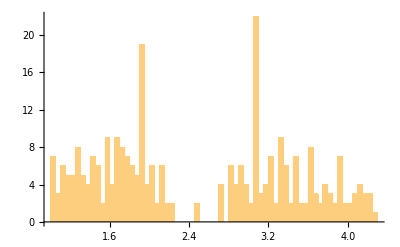

```mathematica
Histogram[Select[Round[ Eigenvalues[I jmat.dmat],0.00001],Positive],80]
```